# Invloed van de grootte geometrie

In dit werkblad wordt de invloed van de grootte (uniform schalen) van de figuur onderzocht. Er wordt verwacht dat de eigenwaarden uniform verkleinen in functie van 1/R met R de schalingsfactor en dat de verhoudingen tussen de eigenwaarden bewaardt blijven.

## Vierkant

```mathematica
Clear["Global`*"]
L = 1;
W = 1;
n = 10;
Ω = 1/Sqrt[2 Pi];
λlist = {{0,0},{1,0},{0,1},{1,1},{2,0},{0,2},{2,1},{1,2},{2,2},{3,0},{0,3},{3,1},{1,3},{3,2},{2,3},{4,0},{0,4},{4,1},{1,4},{3,3}, {4,2},{2,4},{4,3},{3,4},{5,0},{0,5},{5,1},{1,5},{5,2},{2,5},{4,4},{5,3},{3,5},{5,4},{4,5},{5,5}};
eigvals := Table[((Part[Part[λlist,i],1] Pi)/L)^2+((Part[Part[λlist,i],2] Pi)/W)^2, {i, 1, n}];
f[λ_, x_,y_] := Sqrt[2/L]Cos[(Part[λ,1] π)/L(x-L/2)] Sqrt[2/W]Cos[(Part[λ,2] π)/W(y-W/2)] /; Part[λ,1] ≠ 0 && Part[λ,2]≠ 0;
f[λ_, x_,y_] := Sqrt[1/(L W)] /; Part[λ,1] == 0 && Part[λ,2]== 0;
f[λ_, x_,y_] := Sqrt[2/(L W) ] (Cos[(Part[λ,1]  π)/L(x-L/2)] )/; Part[λ,1] ≠ 0 && Part[λ,2]==  0;
f[λ_, x_,y_] := Sqrt[2/(L W)] (Cos[(Part[λ,2]  π)/W(y-W/2)]  )/; Part[λ,1] == 0 && Part[λ,2]≠ 0;
Pm := Table[KroneckerDelta[i,j]   (((Part[Part[λlist,i],1] Pi)/L)^2+((Part[Part[λlist,i],2] Pi)/W)^2), {i, 1, n}, {j,1,n}]
Lm := ParallelTable[Ω^2  NIntegrate[(f[Part[λlist,i], x1,y1] f[Part[λlist,j], x2,y2])/Sqrt[(x1-x2)^2+(y1-y2)^2 +(0.0001)^2],{x1,-L/2,L/2}, {y1,-W/2,W/2},{x2,-L/2,L/2}, {y2,-W/2,W/2},Method->{"GlobalAdaptive", "MaxErrorIncreases"->4000},MinRecursion->30,MaxRecursion->100, PrecisionGoal->6,AccuracyGoal->6],{i,1,n}, {j,1,n}]
```

```mathematica
list = {};
For[i=1,i≤ 40,i++,{L=i*0.1;W=i*0.1; AppendTo[list, Eigenvalues[Lm.Pm]]}]
Export["InvloedGrootteVierkant.csv",list, "CSV"]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

$Aborted

InvloedGrootteVierkant.csv

```mathematica
list = Import["C:\\Users\\frede\\Documents\\Wolfram Mathematica\\Thesis\\data\\InvloedGrootteVierkant.csv"];
```

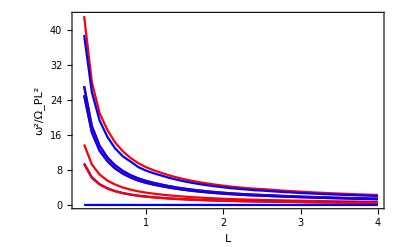

```mathematica
r = Table[(((i)*0.1)),{i,1,40}];
data = Table[Transpose@{r[[2;;40]],list[[2;;40,i]]}, {i,1,10}];
ListPlot[Re[ToExpression[data]],Frame->True,FrameLabel->{{Style["ω^2/Ω_PL^2",Bold,16],""},{Style["L",Bold,16],""}}, Joined->True, PlotRange->Full, PlotStyle->{Red, Blue, Red, Blue,Red,Blue,Red,Blue,Red, Blue}]
```

```mathematica
Re[list[[8,;;]]]
```

{Re[10.760979038620373+0.*I],Re[9.94522393107859+0.*I],Re[6.829838355072961+0.20912949736899483*I],Re[6.829838355072961-0.20912949736899483*I],Re[6.296823592918034+0.*I],Re[6.285223183949977+0.*I],Re[3.5026117917632194+0.*I],Re[2.3918608154368317+0.*I],Re[2.3462551456457+0.*I],Re[0.+0.*I]}

```mathematica
r[[1]]
```

0.1

```mathematica
Lm
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 4000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.000386935 and 0.105816 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 4000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.237725 and 0.103977 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 4000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 4.99886×10^-6 and 0.0893237 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 4000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.00055738 and 0.0779286 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 4000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3.02743 and 0.0991669 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 4000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0295316 and 0.0752875 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 4000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.000587025 and 0.087611 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 4000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.110234 and 0.0849162 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 4000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 4.85143×10^-6 and 0.0713863 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 4000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.000141028 and 0.067324 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 4000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.0000645734 and 0.0894522 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 4000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.0000343369 and 0.0655382 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 4000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.000558034 and 0.0779239 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 4000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.0000579237 and 0.0658934 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 4000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.26152 and 0.0931524 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 4000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.127013 and 0.0758399 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 4000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -4.99886×10^-6 and 0.0893237 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 4000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.0000345943 and 0.0606886 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

{{0.481831,-0.0000102772,-7.95593×10^-7,-2.32419×10^-6,-0.0378306,-0.0378283,-0.0000883807,0.0000884848,0.0047001,-0.0000615827},{7.95593×10^-7,0.200777,-2.32419×10^-6,0.0000315636,-0.000093428,0.0000884848,0.0000224452,-0.0202147,7.03191×10^-6,-0.0175443},{7.95593×10^-7,7.72128×10^-7,0.200777,-0.000031584,-0.0000883807,0.0000645049,-0.0202147,-0.0000224452,5.55183×10^-6,-9.21885×10^-6},{-2.32419×10^-6,0.0000315636,-4.56905×10^-6,0.142904,-0.0000224452,0.0000224452,0.0000220105,-0.0000220105,-0.0000493417,5.014×10^-6},{-0.0378352,-0.000093428,-0.0000888139,0.0000224452,0.13317,0.0047001,5.73896×10^-7,-9.14301×10^-6,-0.0121204,0.0000402721},{-0.0378283,0.0000881557,-0.000093428,0.0000224452,0.00470175,0.13317,-9.16726×10^-6,5.73896×10^-7,-0.0121204,-0.0000649381},{-0.0000887098,0.0000224452,-0.0202147,-8.97082×10^-6,5.73896×10^-7,-5.19502×10^-6,0.110678,0.0000567855,2.81678×10^-6,2.14559×10^-6},{0.0000881557,-0.0202147,-0.0000224452,-0.0000220105,-5.20923×10^-6,5.73896×10^-7,0.0000567855,0.110678,3.41944×10^-6,0.00229497},{0.0047001,-5.46488×10^-6,-5.50586×10^-6,-0.0000198885,-0.0121322,-0.0121004,2.50887×10^-6,-6.01736×10^-6,0.0948755,0.0000141805},{-0.0000615827,-0.0175443,-9.21885×10^-6,5.014×10^-6,0.0000265733,-0.0000649381,-4.11615×10^-6,0.00229497,0.0000142736,0.0968243}}

```mathematica
L
```

1

```mathematica
L=10;W=10;
```

```mathematica
Lm
```

{{4.88542,-0.000429934,-0.000429934,0.000688177,-0.378299,-0.378081,-0.000438641,0.000147969,0.046125,-0.000109069},{-0.000429934,2.08627,-0.0000994809,0.0000861983,-0.000381604,0.000147969,0.00721235,-0.200544,-0.000441508,-0.16686},{-0.000429934,0.000688177,2.08627,-0.000284533,0.000438641,-0.000381604,-0.20075,-0.00721235,0.0010761,0.0000287773},{0.000688177,-0.0000861983,-9.6028×10^-6,1.47199,0.00721235,-0.00721235,-0.000207446,0.000207446,-0.000039961,-0.00029404},{-0.378299,0.000289351,0.000438641,-0.00721235,1.42041,0.0468708,-0.00113895,-0.000441508,-0.118977,0.000597804},{-0.377329,-0.000438641,0.000381604,-0.00721235,0.0464925,1.42041,-0.000441508,0.000537758,-0.118973,-0.000309703},{-0.000147969,-0.00721235,-0.20075,0.000207446,-0.00113895,0.0010761,1.16372,-0.000039961,-0.0000562491,0.000164453},{0.000147969,-0.20075,0.00721235,-0.000393895,0.0010761,0.000537758,0.000205189,1.16372,0.0000562491,0.0216437},{0.0468708,-0.000441508,0.0010761,-0.000205189,-0.119507,-0.121607,0.0000562491,-0.000663964,1.01518,0.000112137},{0.000618434,-0.16686,0.0000287773,-0.00029404,-0.000116555,-0.000309703,-0.000164453,0.0216437,0.000015495,1.02994}}

```mathematica
list[[1]]
```

{85.033,75.5771,53.4659,53.3148,50.0204,49.4812,27.229,18.8181,18.4244,0.}